# Math 350 - Lecture 6

Sums, Products, and Infinity

## Sums and Products

Sum and Products are Mathematica’s implementation of sigma and pi notation.

```mathematica
Sum[a[i], {i, 1, k}]
```

∑_(i=1)^k a[i]

```mathematica
Product[a[i], {i, 1, k}]
```

∏_(i=1)^k a[i]

Usefully, we can use very specific sets to define the index sets for each.

```mathematica
Sum[a[i],{i, Range[2, 10, 2]}]
```

a[2]+a[4]+a[6]+a[8]+a[10]

```mathematica
Product[a[i], {i, Prime/@Range[4]}]
```

a[2] a[3] a[5] a[7]

```mathematica
Sum[a[i], {i, {2, 10, 400}}]
```

a[2]+a[10]+a[400]

Often, the issue turns out to be constructing the function that produces the terms. One thing that can help is to use classical notation by way of the palette menu.

## Term functions

```mathematica
a[i_] := 1/i^2
```

```mathematica
a[3]
```

1/9

```mathematica
Sum[a[i],{i,1,10}]//N
```

1.54977

Consider the problem of finding the sum

∑_(n=1)^10 (1 3 5 ... (2n-1))/(2 5 8 ... (3n-1))

To use Mathematica, we need to write a function to generate the terms, and we need it to depend on n.

```mathematica
2#-1&/@Range[8]
```

{1,3,5,7,9,11,13,15}

```mathematica
3#-1&/@Range[8]
```

{2,5,8,11,14,17,20,23}

```mathematica
Sum[Function[n,Times@@((2#-1)/(3#-1)&@Range[n])][k],{k,1,10}]
```

```mathematica
b[n_]:=Times@@((2#-1)/(3#-1)&@Range[n])
```

```mathematica
Sum[b[n], {n,1,10}]
```

10451099/7982656

## Infinity

Mathematica is reasonably good at handling objects involving infinity.

```mathematica
∞
```

```mathematica
Limit[1/x, x->∞]
```

0

```mathematica
Sum[1/n^2, {n, 1, ∞}]
```

π^2/6

```mathematica
Sum[1/n^3, {n, 1 ,∞}]
```

Zeta[3]

```mathematica
Limit[(1 + 1/n)^n, n-> ∞]
```

ⅇ

You can construct your own explorative limits by using Manipulate.

```mathematica
Manipulate[N[Sum[(-1)^k/k, {k, 1, n}]],{n,1, 10000}]
```

You can also use plots to explore asymptotes.

```mathematica
sumOfReciprocalSquares =Table[{n, N[Sum[1/k^2, {k, 1, n}]]}, {n, 1, 50}];
```

```mathematica
sumOfReciprocalSquares
```

{{1,1.},{2,1.25},{3,1.36111},{4,1.42361},{5,1.46361},{6,1.49139},{7,1.5118},{8,1.52742},{9,1.53977},{10,1.54977},{11,1.55803},{12,1.56498},{13,1.57089},{14,1.576},{15,1.58044},{16,1.58435},{17,1.58781},{18,1.59089},{19,1.59366},{20,1.59616},{21,1.59843},{22,1.6005},{23,1.60239},{24,1.60412},{25,1.60572},{26,1.6072},{27,1.60857},{28,1.60985},{29,1.61104},{30,1.61215},{31,1.61319},{32,1.61417},{33,1.61509},{34,1.61595},{35,1.61677},{36,1.61754},{37,1.61827},{38,1.61896},{39,1.61962},{40,1.62024},{41,1.62084},{42,1.62141},{43,1.62195},{44,1.62246},{45,1.62296},{46,1.62343},{47,1.62388},{48,1.62432},{49,1.62473},{50,1.62513}}

```mathematica
p1 = ListPlot[sumOfReciprocalSquares];
```

```mathematica
p2 = Plot[Pi^2/6, {n, 1, 50},PlotStyle->Red];
```

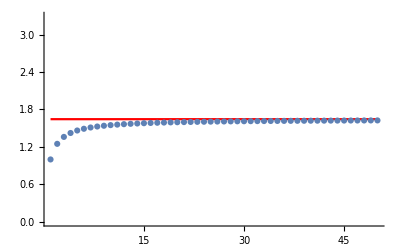

```mathematica
Show[p2, p1]
```

```mathematica
harmonicSum = Table[{n, Sum[1/k, {k,1,n}]}, {n, 1, 4000}];
```

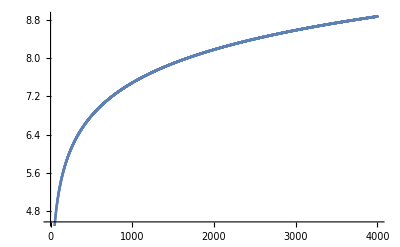

```mathematica
ListPlot[harmonicSum]
```

## What We Covered

Sum, Product
Term functions
Infinity/asymptotics
Show